1/2

0.001

0.1

0.25 (-3-ⅇ^(-0.2 t)+4 ⅇ^(-0.1 t)+0.2 t)

1

0.001

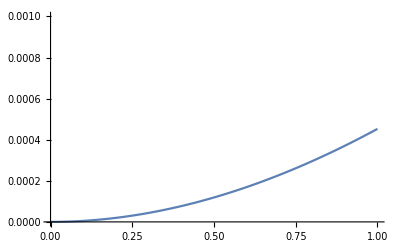

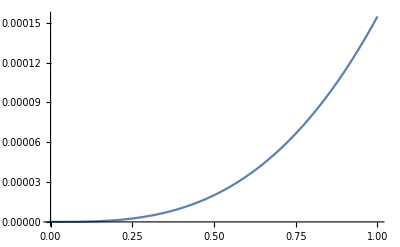

```mathematica
vo = 5 10^-4/10^-3
d = 0.001
α = 0.1
β[t_]=(vo^2 d)/α^3(2 α t - Exp[-2 α t] + 4 Exp[-α t]-3)
xmax = 1
ymax = 0.001
(*Plot[β[t],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]*)
Plot[Evaluate[D[β[t],t]],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]
Plot[β[t],{t,0,xmax},PlotRange->All]
```

```mathematica
Sqrt[β[1]]
```

0.012439

```mathematica
thetCorr[s_,t_]= df/αf(Exp[-αf (t-s)]-Exp[-αf (t+s)])
yThetCorr = vof Integrate[thetCorr[s,t],{s,0,t}]//Expand
betF = 2vof Integrate[yThetCorr,{t,0,T}]
```

(df (ⅇ^(-((-s+t) αf))-ⅇ^(-((s+t) αf))))/αf

(df vof)/αf^2+(df ⅇ^(-2 t αf) vof)/αf^2-(2 df ⅇ^(-t αf) vof)/αf^2

-(df vof^2 (3+ⅇ^(-2 T αf)-4 ⅇ^(-T αf)-2 T αf))/αf^3